## Solution CP8: Partial derivatives and multivariate functions

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Partial derivatives

In Mathematica, the command D[f,x] is also used for calculating first and second partial derivatives of a multivariate function. A special form of this command D[f,{{x,y},2}] will calculate the Hessian of the function f, i.e., a representation of the second partial derivatives (∂^2 f)/(∂x^2), (∂^2 f)/(∂y^2), (∂^2 f)/(∂x∂y) and (∂^2 f)/(∂y∂x).

### Exercise 8-1: Partial derivatives

Calculate the partial derivatives (∂f)/(∂x), (∂f)/(∂y),  (∂^2 f)/(∂x^2), (∂^2 f)/(∂y^2), (∂^2 f)/(∂x∂y) and (∂^2 f)/(∂y∂x) for the following functions:

(a) f(x,y)=x ·cos(2y)

```mathematica
f=x*Cos[2*y]
D[f,x]
D[f,y]
MatrixForm[D[f,{{x,y},2}]]
```

x Cos[2 y]

Cos[2 y]

-2 x Sin[2 y]

(0 | -2 Sin[2 y]
-2 Sin[2 y] | -4 x Cos[2 y])

(b) f(x,y)=x/(x+y)

```mathematica
f=x/(x+y)
Simplify[D[f,x]]
Simplify[D[f,y]]
MatrixForm[Simplify[D[f,{{x,y},2}]]]
```

x/(x+y)

y/(x+y)^2

-x/(x+y)^2

(-(2 y)/(x+y)^3 | (x-y)/(x+y)^3
(x-y)/(x+y)^3 | (2 x)/(x+y)^3)

(c) f(x,y)=ln(x-y)

```mathematica
f=Log[x-y]
D[f,x]
D[f,y]
MatrixForm[D[f,{{x,y},2}]]
```

Log[x-y]

1/(x-y)

-1/(x-y)

(-1/(x-y)^2 | 1/(x-y)^2
1/(x-y)^2 | -1/(x-y)^2)

(d) f(x,y)=e^(2x-3y)

```mathematica
f=Exp[2*x-3*y]
D[f,x]
D[f,y]
MatrixForm[D[f,{{x,y},2}]]
```

ⅇ^(2 x-3 y)

2 ⅇ^(2 x-3 y)

-3 ⅇ^(2 x-3 y)

(4 ⅇ^(2 x-3 y) | -6 ⅇ^(2 x-3 y)
-6 ⅇ^(2 x-3 y) | 9 ⅇ^(2 x-3 y))

### Exercise 8-2: Extremes of a multivariate function

(a) Calculate the optimal conditions, i.e., the temperature x (°C) and relative humidity y (%) that maximize the survival v(x,y)=4y-0.05·(x+x^2-xy+y^2) of the blue poison arrow frog Dendrobatus azureus.

```mathematica
v=4*y-0.05*(x+x^2-x*y+y^2);
Values[Solve[{D[v,x]==0,D[v,y]==0},{x,y}]]
```

{{26.,53.}}

Taking the first partial derivatives and solving for  (∂f)/(∂x)=0 and(∂f)/(∂y)=0 yields the extremum (x=26, y=53), or a temperature of 26°C in combination with a relative humidity of 53%.

```mathematica
H=D[v,{{x,y},2}];
MatrixForm[H]
Det[H]
```

(-0.1 | 0.05
0.05 | -0.1)

0.0075

Analyzing the second partial derivatives shows that the extremum (26,53) is not a saddle point, since the determinant of the Hessian 0.0075 > 0. The extremum (26,53) is indeed a maximum, as the element on the main diagonal of the Hessian are < 0.

(b) Plot the survival function v(x,y). Hint: use the command Plot3D[].

```mathematica
Plot3D[v,{x,0,40},{y,0,100},BoxRatios->{1,1,1},ColorFunction->ColorData["Rainbow"]]
```

-Graphics3D-

### Exercise 8-3: Error analysis

The function S(V,d)=5000·V/d^2 describes the wind speed S (m/s) at a distance d  (m) of the eye of a hurricane with volume V (m^3). Consider a hurricane with volume V̄= 6·10^4±1·10^4 m^3 at a distance d̄=3·10^3±1·10^3 m (mean ± stddev)

(a) Estimate the expected wind speed S̄ in km/h from S(V,d). Assuming that wind speeds > 200 km/h can be dangerous, would you evacuate the inhabitants?

```mathematica
hurricane={V->60000,d->3000,sdV->10000,sdd->1000};
S=5000*V/d^2
S1=N[S]/.hurricane
S1km=((60*60)/1000)*S1
```

(5000 V)/d^2

33.3333

120.

120 km/h << 200 km/h, so evacuation is not necessary.

(b) Now use the improved estimator  S̄=S(V,d)+1/2·(∂^2 S)/(∂V^2)·(SD(V))^2+1/2·(∂^2 Sf)/(∂d^2)·(SD(d))^2. How about evacuation in this case?

```mathematica
SV=D[S,V]
Sd=D[S,d]
S2V=D[S,V,V]
S2d=D[S,d,d]
S2=N[(S+(1/2)*S2V*sdV^2+(1/2)*S2d*sdd^2)]/.hurricane
S2km=((60*60)/1000)*S2
```

5000/d^2

-(10000 V)/d^3

0

(30000 V)/d^4

44.4444

160.

160 km/h < 200 km/h, so evacuation is not necessary.

(c) Also estimate the std deviation of wind speed SD(S)=√(((∂S)/(∂V)·SD(V))^2+((∂S)/(∂d)·SD(d))^2). Are you going to evacuate now?

```mathematica
sdS=N[Sqrt[(SV*sdV)^2+(Sd*sdd)^2]]/.hurricane
sdSkm=((60*60)/1000)*sdS
```

22.9061

82.4621

The expected wind speed S̄±SD(S) = 160 ± 82 km/h. Assuming a normal distribution, there is a probability of ca. 16% that wind speeds will be > 242 km/h, so evacuation might be a good idea after all.

(d) Let us see whether error analysis works well. Draw a large (e.g. 10000) number of random normal variables for V and for d. Compute S(V,d) for each of these random variables, and compare the mean and std deviation to your estimates in (b) and (c). Are they similar? What is the probability that the wind speed exceeds 200 km/h?  Hint: use the Mathematica commands RandomVariate[distr, n] to draw n samples from distribution dist,  NormalDistribution[mean, std] to define a normal distribution with mean mean and standard deviation std and Histogram[] to plot a histogram of the generated values.

```mathematica
distV=RandomVariate[NormalDistribution[60000, 10000], 10000000];
distd=RandomVariate[NormalDistribution[3000, 1000],10000000];
distS=3.6*5000*distV/distd^2;
```

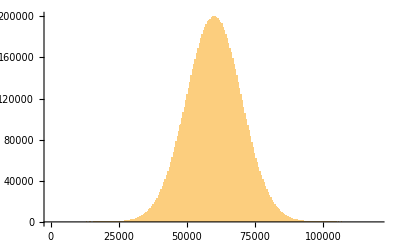

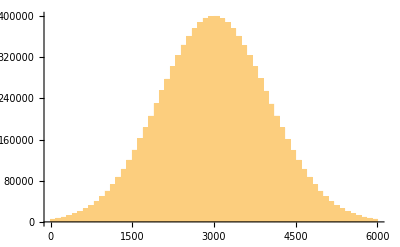

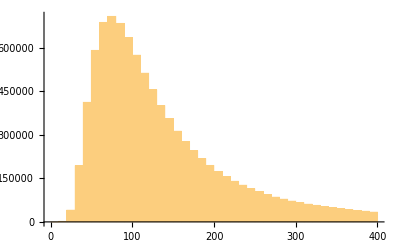

631094.

119.268

7.2784×10^8

200.555

```mathematica
Histogram[distV,{0,120000,500}]
Histogram[distd,{0,6000,100}]
Histogram[distS,{0,400,10}]
Mean[distS]
Median[distS]
StandardDeviation[distS]
Quantile[distS,0.75]
```